```mathematica
(* Simple function for joining four matrices into one *)join4[a_,b_,c_,d_]:=Join[Join[a,b,2], Join[c,d,2]]
```

```mathematica
(* Some random data *)
m={{17,14,1,16,20,6,2,11},{14,9,4,10,6,16,17,13},{3,7,17,11,10,5,2,16},{6,12,15,13,19,7,13,20},{13,19,2,13,6,8,10,8},{10,8,13,15,2,15,12,11},{20,13,17,20,20,2,14,3},{8,12,2,19,15,14,8,16}};
MatrixForm[m]
```

(17 | 14 | 1 | 16 | 20 | 6 | 2 | 11
14 | 9 | 4 | 10 | 6 | 16 | 17 | 13
3 | 7 | 17 | 11 | 10 | 5 | 2 | 16
6 | 12 | 15 | 13 | 19 | 7 | 13 | 20
13 | 19 | 2 | 13 | 6 | 8 | 10 | 8
10 | 8 | 13 | 15 | 2 | 15 | 12 | 11
20 | 13 | 17 | 20 | 20 | 2 | 14 | 3
8 | 12 | 2 | 19 | 15 | 14 | 8 | 16)

```mathematica
(* 1-step transform of the 2-d array *)
rules=Normal[DiscreteWaveletTransform[m,HaarWavelet[],1]]
```

{{0}→{{27.,15.5,24.,21.5},{14.,28.,20.5,25.5},{25.,21.5,15.5,20.5},{26.5,29.,25.5,20.5}},{1}→{{4.,-10.5,2.,-2.5},{-5.,4.,8.5,-10.5},{-2.,-6.5,-7.5,1.5},{1.5,-10.,9.5,1.5}},{2}→{{4.,1.5,2.,-8.5},{-4.,0.,-5.5,-7.5},{7.,-6.5,-1.5,-2.5},{6.5,8.,-3.5,-3.5}},{3}→{{-1.,-4.5,12.,-6.5},{1.,2.,-3.5,-3.5},{-4.,-4.5,5.5,0.5},{5.5,7.,8.5,9.5}}}

```mathematica
(* Show the result as a matrix *)
MatrixForm[join4[{0}/.rules, {1}/.rules, {2}/.rules, {3}/.rules]]
```

(27. | 15.5 | 24. | 21.5 | 4. | -10.5 | 2. | -2.5
14. | 28. | 20.5 | 25.5 | -5. | 4. | 8.5 | -10.5
25. | 21.5 | 15.5 | 20.5 | -2. | -6.5 | -7.5 | 1.5
26.5 | 29. | 25.5 | 20.5 | 1.5 | -10. | 9.5 | 1.5
4. | 1.5 | 2. | -8.5 | -1. | -4.5 | 12. | -6.5
-4. | 0. | -5.5 | -7.5 | 1. | 2. | -3.5 | -3.5
7. | -6.5 | -1.5 | -2.5 | -4. | -4.5 | 5.5 | 0.5
6.5 | 8. | -3.5 | -3.5 | 5.5 | 7. | 8.5 | 9.5)

```mathematica
(* 2-step transform *)
rules=Normal[DiscreteWaveletTransform[m,HaarWavelet[],2]]
```

{{0}→{{27.,15.5,24.,21.5},{14.,28.,20.5,25.5},{25.,21.5,15.5,20.5},{26.5,29.,25.5,20.5}},{1}→{{4.,-10.5,2.,-2.5},{-5.,4.,8.5,-10.5},{-2.,-6.5,-7.5,1.5},{1.5,-10.,9.5,1.5}},{2}→{{4.,1.5,2.,-8.5},{-4.,0.,-5.5,-7.5},{7.,-6.5,-1.5,-2.5},{6.5,8.,-3.5,-3.5}},{3}→{{-1.,-4.5,12.,-6.5},{1.,2.,-3.5,-3.5},{-4.,-4.5,5.5,0.5},{5.5,7.,8.5,9.5}},{0,0}→{{42.25,45.75},{51.,41.}},{0,1}→{{-1.25,-1.25},{0.5,0.}},{0,2}→{{0.25,-0.25},{-4.5,-5.}},{0,3}→{{12.75,3.75},{3.,-5.}}}

```mathematica
(* Show the result as a matrix *)
mout=join4[{0,0}/.rules, {0,1}/.rules, {0,2}/.rules, {0,3}/.rules];
mout = join4[mout, {1}/.rules, {2}/.rules, {3}/.rules];
MatrixForm[mout]
```

(42.25 | 45.75 | -1.25 | -1.25 | 4. | -10.5 | 2. | -2.5
51. | 41. | 0.5 | 0. | -5. | 4. | 8.5 | -10.5
0.25 | -0.25 | 12.75 | 3.75 | -2. | -6.5 | -7.5 | 1.5
-4.5 | -5. | 3. | -5. | 1.5 | -10. | 9.5 | 1.5
4. | 1.5 | 2. | -8.5 | -1. | -4.5 | 12. | -6.5
-4. | 0. | -5.5 | -7.5 | 1. | 2. | -3.5 | -3.5
7. | -6.5 | -1.5 | -2.5 | -4. | -4.5 | 5.5 | 0.5
6.5 | 8. | -3.5 | -3.5 | 5.5 | 7. | 8.5 | 9.5)

```mathematica
(* 3-step transform *)
rules=Normal[DiscreteWaveletTransform[m,HaarWavelet[],3]]
```

{{0}→{{27.,15.5,24.,21.5},{14.,28.,20.5,25.5},{25.,21.5,15.5,20.5},{26.5,29.,25.5,20.5}},{1}→{{4.,-10.5,2.,-2.5},{-5.,4.,8.5,-10.5},{-2.,-6.5,-7.5,1.5},{1.5,-10.,9.5,1.5}},{2}→{{4.,1.5,2.,-8.5},{-4.,0.,-5.5,-7.5},{7.,-6.5,-1.5,-2.5},{6.5,8.,-3.5,-3.5}},{3}→{{-1.,-4.5,12.,-6.5},{1.,2.,-3.5,-3.5},{-4.,-4.5,5.5,0.5},{5.5,7.,8.5,9.5}},{0,0}→{{42.25,45.75},{51.,41.}},{0,1}→{{-1.25,-1.25},{0.5,0.}},{0,2}→{{0.25,-0.25},{-4.5,-5.}},{0,3}→{{12.75,3.75},{3.,-5.}},{0,0,0}→{{90.}},{0,0,1}→{{3.25}},{0,0,2}→{{-2.}},{0,0,3}→{{-6.75}}}

```mathematica
mout=join4[{0,0,0}/.rules, {0,0,1}/.rules, {0,0,2}/.rules, {0,0,3}/.rules];
mout = join4[mout, {0,1}/.rules, {0,2}/.rules, {0,3}/.rules];
mout = join4[mout, {1}/.rules, {2}/.rules, {3}/.rules];
MatrixForm[mout]
```

(90. | 3.25 | -1.25 | -1.25 | 4. | -10.5 | 2. | -2.5
-2. | -6.75 | 0.5 | 0. | -5. | 4. | 8.5 | -10.5
0.25 | -0.25 | 12.75 | 3.75 | -2. | -6.5 | -7.5 | 1.5
-4.5 | -5. | 3. | -5. | 1.5 | -10. | 9.5 | 1.5
4. | 1.5 | 2. | -8.5 | -1. | -4.5 | 12. | -6.5
-4. | 0. | -5.5 | -7.5 | 1. | 2. | -3.5 | -3.5
7. | -6.5 | -1.5 | -2.5 | -4. | -4.5 | 5.5 | 0.5
6.5 | 8. | -3.5 | -3.5 | 5.5 | 7. | 8.5 | 9.5)

```mathematica
(* Symbolic transform *)
m2 = {a,b,c,d,e,f,g,h};
rules2=Normal[DiscreteWaveletTransform[m2,HaarWavelet[],1]]
```

{{0}→{0.707107 a+0.707107 b,0.707107 c+0.707107 d,0.707107 e+0.707107 f,0.707107 g+0.707107 h},{1}→{0.707107 a-0.707107 b,0.707107 c-0.707107 d,0.707107 e-0.707107 f,0.707107 g-0.707107 h}}

```mathematica
(* Try an image *)
image=Import[StringJoin[NotebookDirectory[] ,"Images/lenna256.jpg"]]
```

-Graphics-

```mathematica
dwt=DiscreteWaveletTransform[image,HaarWavelet[],1]
dwt[All,"Image"]
dwt2=DiscreteWaveletTransform[image,HaarWavelet[],2]
dwt2[All,"Image"]
```

DiscreteWaveletData[«DWT»,<1>,{256,256}]

{{0}→-Graphics-,{1}→-Graphics-,{2}→-Graphics-,{3}→-Graphics-}

DiscreteWaveletData[«DWT»,<2>,{256,256}]

{{0}→-Graphics-,{1}→-Graphics-,{2}→-Graphics-,{3}→-Graphics-,{0,0}→-Graphics-,{0,1}→-Graphics-,{0,2}→-Graphics-,{0,3}→-Graphics-}

```mathematica
linear = {17,14,1,16,20,6,2,11}
```

{17,14,1,16,20,6,2,11}

```mathematica
rules=Normal[DiscreteWaveletTransform[linear,HaarWavelet[],1]]
```

{{0}→{21.9203,12.0208,18.3848,9.19239},{1}→{2.12132,-10.6066,9.89949,-6.36396}}

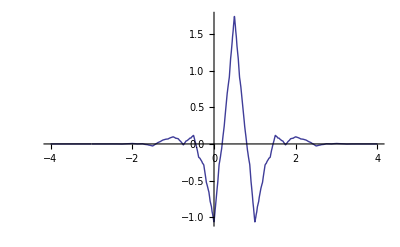

```mathematica
Plot[WaveletPsi[CDFWavelet[],x],{x,-4, 4},PlotRange->All]
```

```mathematica
WaveletFilterCoefficients[CDFWavelet["9/7"],{"PrimalLowpass","PrimalHighpass"}]
```

{{{-4,0.0267488},{-3,-0.0168641},{-2,-0.0782233},{-1,0.266864},{0,0.602949},{1,0.266864},{2,-0.0782233},{3,-0.0168641},{4,0.0267488}},{{-2,0.0456359},{-1,-0.0287718},{0,-0.295636},{1,0.557544},{2,-0.295636},{3,-0.0287718},{4,0.0456359}}}

```mathematica
Normal[DiscreteWaveletTransform[m,HaarWavelet[],1]]
```

{{0}→{{27.,15.5,24.,21.5},{14.,28.,20.5,25.5},{25.,21.5,15.5,20.5},{26.5,29.,25.5,20.5}},{1}→{{4.,-10.5,2.,-2.5},{-5.,4.,8.5,-10.5},{-2.,-6.5,-7.5,1.5},{1.5,-10.,9.5,1.5}},{2}→{{4.,1.5,2.,-8.5},{-4.,0.,-5.5,-7.5},{7.,-6.5,-1.5,-2.5},{6.5,8.,-3.5,-3.5}},{3}→{{-1.,-4.5,12.,-6.5},{1.,2.,-3.5,-3.5},{-4.,-4.5,5.5,0.5},{5.5,7.,8.5,9.5}}}

```mathematica
Normal[LiftingWaveletTransform[m,HaarWavelet[],1]]
```

{{0}→{{27.,15.5,24.,21.5},{14.,28.,20.5,25.5},{25.,21.5,15.5,20.5},{26.5,29.,25.5,20.5}},{1}→{{-4.,10.5,-2.,2.5},{5.,-4.,-8.5,10.5},{2.,6.5,7.5,-1.5},{-1.5,10.,-9.5,-1.5}},{2}→{{-4.,-1.5,-2.,8.5},{4.,0.,5.5,7.5},{-7.,6.5,1.5,2.5},{-6.5,-8.,3.5,3.5}},{3}→{{-1.,-4.5,12.,-6.5},{1.,2.,-3.5,-3.5},{-4.,-4.5,5.5,0.5},{5.5,7.,8.5,9.5}}}

```mathematica
Normal[LiftingWaveletTransform[{0,0,0,0,0,1,0,0,0,0,0,0},CDFWavelet[],1]]
```

{{0}→{0.,-0.0238495,0.377403,0.377403,-0.0238495,0.},{1}→{0.,-0.0406894,0.788486,-0.0406894,0.,0.}}

```mathematica
Normal[LiftingWaveletTransform[{0,0,0,0,0,0,1,0,0,0,0,0},CDFWavelet[],1]]
```

{{0}→{0.,0.0378285,-0.110624,0.852699,-0.110624,0.0378285},{1}→{0.,0.0645389,-0.418092,-0.418092,0.0645389,0.}}

```mathematica
Normal[LiftingWaveletTransform[{0,0,0,0,0,5,9,2,3,0,0,0,0,0},CDFWavelet[],1]]
```

{{0}→{0.,0.221209,0.957181,9.98423,2.19803,-0.039116,0.113485},{1}→{0.,0.377403,0.291835,-3.64358,-0.754806,0.193617,0.}}

```mathematica
Normal[LiftingWaveletTransform[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},CDFWavelet[],1]]
```

{{0}→{5.90633,4.4663,7.07107,9.89949,12.7279,15.5563,17.7795,22.7595},{1}→{0.381591,0.,0.,0.,6.18076×10^-15,0.,-1.03262,6.30788}}

```mathematica
Normal[DiscreteWaveletTransform[{7,2,3,4,5,3,1,5,7,1,9,2,4,8,2,6},CDFWavelet[],1,Padding->Reflected]]
```

{{0}→{6.82547,3.52709,7.00224,3.52709,6.82547,2.87912,7.34827,7.39307,6.14146,6.57857,6.57857,6.14146},{1}→{-0.122068,2.33178,2.33178,-0.122068,-0.136087,-1.33848,5.86312,3.64358,-4.18374,-2.92382,-4.18374,3.64358}}

```mathematica
Normal[DiscreteWaveletTransform[{7,2,3,4,5,3,1,5,7,1,9,2,4,8,2,6},CDFWavelet[],2,Padding->Reflected]]
```

{{0}→{6.82547,3.52709,7.00224,3.52709,6.82547,2.87912,7.34827,7.39307,6.14146,6.57857,6.57857,6.14146},{1}→{-0.122068,2.33178,2.33178,-0.122068,-0.136087,-1.33848,5.86312,3.64358,-4.18374,-2.92382,-4.18374,3.64358},{0,0}→{6.88035,7.51302,7.28125,7.51302,6.88035,8.98088,9.26102,9.18004,9.18004,9.26102},{0,1}→{2.34611,2.39481,2.39481,2.34611,3.25184,-0.669628,-0.217068,0.401068,-0.217068,-0.669628}}

```mathematica
N[Solve[1+2x+5/2 x^2+5/2 x^3==0,x],20]
```

{{x→-0.6847681897167382634},{x→-0.1576159051416308683+0.74786129086722024522 ⅈ},{x→-0.1576159051416308683-0.74786129086722024522 ⅈ}}

```mathematica
1/-0.684768189716738263398607308005563374387323827368885595501
```

-1.4603482098280014583601126326608942037436609421600391468

```mathematica
c=1/-0.68476818971673826339;
Solve[(1+2x+5/2 x^2+5/2 x^3)/(1-c x)==0,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.1576159051416308683-0.7478612908672202452 ⅈ},{x→-0.1576159051416308683+0.7478612908672202452 ⅈ}}

```mathematica
data1={10, 20, 30, 40};
data2={12, 17, 35, 50};
mse = Sum[Abs[data1[[i]]-data2[[i]]], {i, Length[data1]}]/Length[data1] //N
mse = Sum[(data1[[i]]-data2[[i]])^2, {i, Length[data1]}]/Length[data1] //N
psnr = 20 Log10[255]-10 Log10[mse]
```

5.

34.5

32.7526